```mathematica
Análisis

Se analiza el grafo resultante de una simulación del modelo en NetLogo.

Parametros de la simulación

Capacity:3
Agents     : 300
Ticks         :3000
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
findVertexDegreeLimit[maxconnection_,percentage_]:=(maxconnection*percentage)/100;
```

```mathematica
findHubs[graph_,percentage_]:=Module[{limit=findVertexDegreeLimit[Max[VertexDegree[graph]],percentage],hubs={}},
For[i=1,i≤VertexCount[graph],i++,If[VertexDegree[graph,i]≥limit,hubs=Append[hubs,i],Null]];
Return[hubs]
];
```

### Carga del grafo generado en la simulación

```mathematica
red=Import["Redes/network-300-3-3000.g6"];
```

### Hubs identificados cuando el grado de vértice excede el 90 por ciento del máximo.

```mathematica
hubsFound=findHubs[red,90];
```

```mathematica
hubsFound
```

{50,190,291}

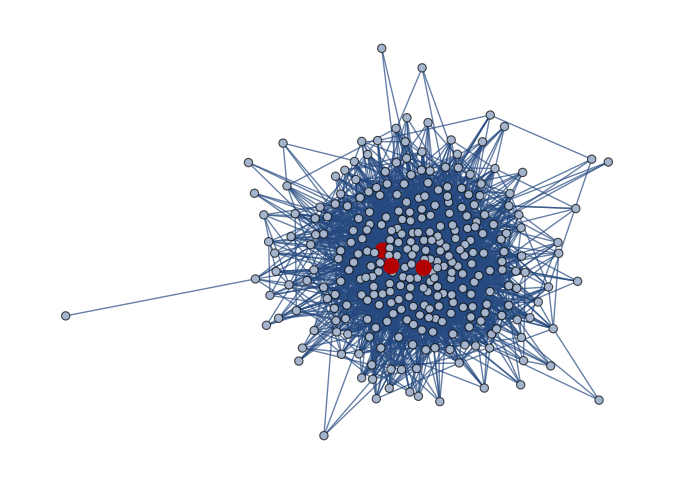

```mathematica
HighlightGraph[red,hubsFound,VertexSize->Thread[hubsFound->3]]
```

```mathematica
Medidas de Centralidad
```

```mathematica
Part[VertexList[red],Ordering[ClosenessCentrality[red],All,Greater]]
```

{190,291,247,79,50,162,265,128,60,122,280,92,51,258,116,152,68,168,139,199,187,38,178,53,42,148,21,9,286,185,41,28,11,214,25,261,197,149,75,22,213,105,232,172,175,123,71,17,290,257,220,74,62,94,241,163,239,235,205,198,243,155,126,57,35,282,271,255,106,217,195,31,19,202,200,183,287,252,180,157,47,296,240,158,34,2,226,251,184,283,40,39,27,16,270,277,167,294,186,107,272,173,170,137,1,171,127,196,142,118,110,219,188,76,10,109,65,67,203,131,250,193,58,108,78,268,159,222,248,150,225,146,143,129,18,295,3,274,91,212,210,300,260,133,278,64,256,182,93,154,86,119,292,135,249,242,114,100,37,97,13,99,83,201,176,136,275,120,98,95,140,61,14,229,103,46,289,279,231,26,147,84,85,15,254,63,52,276,245,165,111,80,160,174,164,24,288,264,144,117,269,7,43,299,115,29,273,113,54,216,169,233,33,263,224,73,88,69,12,293,223,181,104,192,161,130,125,237,70,5,23,177,246,234,236,151,20,208,44,298,132,259,215,49,191,221,30,253,189,81,112,285,96,153,266,206,238,55,121,32,227,48,87,211,284,36,89,228,218,82,141,8,102,138,134,179,77,90,209,267,4,66,262,194,101,72,207,297,230,281,56,59,166,124,244,156,145,45,204,6}

```mathematica
Part[VertexList[red],Ordering[BetweennessCentrality[red],All,Greater]]
```

{291,190,50,79,199,152,247,280,168,122,265,139,28,128,286,162,21,116,220,92,51,187,60,257,53,41,75,17,198,106,252,213,178,251,241,277,148,74,258,68,283,149,197,163,9,282,71,232,261,38,57,11,157,105,243,239,183,255,214,172,126,90,123,202,180,19,271,205,22,42,217,107,200,142,175,34,25,35,158,155,296,67,185,31,118,235,110,58,127,62,184,137,173,100,186,290,195,39,167,86,268,47,94,170,2,240,294,27,171,14,16,203,10,40,226,225,182,222,146,159,143,108,272,65,78,1,76,292,84,147,131,287,109,193,119,91,256,270,300,188,196,274,208,210,289,125,3,114,97,295,18,219,13,144,133,140,93,103,130,150,249,52,260,153,288,201,85,70,299,64,273,43,176,248,80,136,154,46,37,229,61,24,15,99,83,169,95,87,279,250,245,135,237,242,231,120,129,113,233,276,212,263,223,275,161,30,117,174,160,181,63,269,49,33,164,253,98,189,26,69,264,88,259,23,5,216,81,138,236,12,77,254,246,234,177,29,36,278,104,54,111,192,151,96,73,293,44,48,102,298,262,112,20,66,191,218,165,82,132,267,238,134,7,221,227,72,194,4,89,215,115,228,206,55,121,224,8,56,266,297,284,179,156,124,285,244,141,32,101,209,281,45,207,211,204,59,145,230,166,6}

### La medida de centralidad de cercanía nos muestra que el nodo hub 190 tiene una característica muy importante de integración pues a través de el fluye o se distribuye la información de manera más eficiente; ya que es el nodo capaz de conectar cualquier nodo de la red de manera más rápida. La medida de intermediación de la red nos permite interpretar al nodo hub 291 como un agente de control y regulación que puede ser el lider que influya en la coordinación de la red. Se observa que en las dos medidas de centralidad realizadas sobre el grafo para la caracterización, dentro del top 5 de los más altos valores se encuentran los nodos con más alto grado de conectividad hallados inicialmente.

```mathematica
CommunityGraphPlot[red,FindGraphCommunities[red,Method->"Modularity"]]
```

#### Comunidades de nodos generados con el método de partición “modularity”.

-Graphics-

Grado de conexión de un nodo dentro de su módulo. zScore mide el grado de conexión de un nodo i respecto al resto de nodos pertenecientes a su mismo módulo:
node: el nodo i, al que se le calcula el grado de conectividad intramodular
modules: Lista de módulos o comunidades generados por el modularity
graph: La red que se analizará

```mathematica
zScore[node_,modules_,graph_]:=Module[{
nodeModuleList=Select[modules,MemberQ[#,node]&][[1]],
nodeModuleGraph,vertexDegreeModule,ki,ksi,result
},
nodeModuleGraph=Subgraph[graph,nodeModuleList];
vertexDegreeModule=VertexDegree[nodeModuleGraph];
ki=VertexDegree[nodeModuleGraph,node];
ksi=Mean[vertexDegreeModule];
result=(ki-ksi)/StandardDeviation[vertexDegreeModule];
Return[result]
];
```

participationCoefficient: El coeficiente de participación de un nodo i cualquiera mide como es su participación con nodos intermodulares. el coeficiente estará muy cercano a 1 si se relaciona de manera mas o menos uniforme con otros módulos y será 0 si solo se vincula con nodos de su mismo módulo.
node: el nodo i, al que se le calcula el coeficiente de participación
modules: Lista de módulos o comunidades generados por el modularity
graph: La red que se analizará

```mathematica
participationCoefficient[node_,modules_,graph_]:=Module[{
suma=0,
neighborsList=VertexList[NeighborhoodGraph[graph,node]]/. node->Nothing
},
For[s=1,s≤Length[modules],s++,
kis=Length[Intersection[neighborsList,modules[[s]]]];
ki=VertexDegree[graph,node];
suma=suma+(kis/ki)^2;
];
suma=1-suma;
Return[suma]
];
```

getCharacterizationMatrix: genera una matriz o lista de listas donde el primer elemento de la lista corresponde a las medidas de conectividad intramodular (zScore) y de participación intermodular (participationCoefficient) --> {{zScore[1],pCoeff[1]},...,{zScore[n],pCoeff[n]}} donde n es el número total de nodos de la red.
graph: La red que le entra para caracterizar los nodos.

```mathematica
getCharacterizationMatrix[graph_]:=Module[{
modules=FindGraphCommunities[graph,Method->"Modularity"],
characterizationMatrix={}
},
For[node=1,node≤VertexCount[graph],node++,
characterizationMatrix=Join[characterizationMatrix,{{zScore[node,modules,graph],participationCoefficient[node,modules,graph]}}]
];
Return[characterizationMatrix];
];
```

```mathematica
cMatrix=getCharacterizationMatrix[red];
```

isHub: determina basado en la medida zScore si un nodo puede ser caracterizado como hub o no.
list: es un lista dupla con el formato {zScore[n],pCoeff[n]}

```mathematica
isHub[list_]:=Module[{},
If[list[[1]]≥2.5,"module-hubs","non-hubs"]
];
```

getHubClasificationLists: devuelve una lista de dos elementos, el primer elemento de la lista representa una lista con todos los nodos caracterizados como hubs y en el segundo el resto de nodos no hubs.
data: los datos de las medidas de cada nodo: {{zScore[1],pCoeff[1]},...,{zScore[n],pCoeff[n]}}

```mathematica
getHubClasificationLists[data_]:=Module[{
clasificationList=Map[isHub,data],
hubList, nonHubList,resultList={}
},
hubList=Flatten[Position[clasificationList,_?(#=="module-hubs"&)]];
nonHubList=Complement[Range[Length[data]],hubList];
resultList={hubList,nonHubList};
Return[resultList]
];
```

```mathematica
classificatedHubs=getHubClasificationLists[cMatrix][[1]];
```

```mathematica
classificatedHubs
```

{75,190,252,265}

```mathematica
VertexDegree[red,265]
```

49

classifyRole: recibe las medidas de zScore y participationCoefficient de un nodo y los clasifica de acuerdo a su caracterización en uno de los roles universales definidos R1,R2,R3,R4,R5,R6,R7
dataNode: {zScore[n],pCoeff[n]}

```mathematica
classifyRole[dataNode_]:=Module[{zScore,pCoef, role},
zScore=dataNode[[1]];
pCoef=dataNode[[2]];
role=Which[zScore<2.5,
Which[
pCoef==0,"R1",
0<pCoef<0.62,"R2",
0.62<=pCoef<0.80,"R3",
pCoef≥0.8,"R4"
],
zScore≥2.5,
Which[
0≤pCoef≤0.3,"R5",
0.3<pCoef<0.75,"R6",
pCoef≥0.75,"R7"]
];
Return[role]
];
```

getHubRoleList: devuelve una lista de nodos hub con su respectiva asociación a su rol universal.
characterizationMatrix: lista de listas o matriz del tipo  {{zScore[1],pCoeff[1]},...,{zScore[n],pCoeff[n]}}

```mathematica
getHubRoleList[characterizationMatrix_]:=Module[{
hubRoleList={},
hubsList=getHubClasificationLists[characterizationMatrix][[1]]
},
For[i=1,i≤Length[hubsList],i++,
hubRoleList=Join[hubRoleList,{hubsList[[i]]->classifyRole[characterizationMatrix[[hubsList[[i]]]]]}];
];
Return[hubRoleList]
];
```

```mathematica
getHubRoleList[cMatrix]
```

{75→R6,190→R6,252→R6,265→R6}

getNonHubRoleList: devuelve una lista de nodos no hubs con su respectiva asociación a su rol universal.
characterizationMatrix: lista de listas o matriz del tipo  {{zScore[1],pCoeff[1]},...,{zScore[n],pCoeff[n]}}

```mathematica
getNonHubRoleList[characterizationMatrix_]:=Module[{
nonHubRoleList={},
nonHubsList=getHubClasificationLists[characterizationMatrix][[2]]
},
For[i=1,i≤Length[nonHubsList],i++,
nonHubRoleList=Join[nonHubRoleList,{nonHubsList[[i]]->classifyRole[characterizationMatrix[[nonHubsList[[i]]]]]}];
];
Return[nonHubRoleList]
];
```

```mathematica
getNonHubRoleList[cMatrix]
```

{1→R3,2→R2,3→R3,4→R2,5→R2,6→R1,7→R2,8→R2,9→R3,10→R3,11→R2,12→R2,13→R3,14→R2,15→R2,16→R3,17→R3,18→R3,19→R3,20→R2,21→R3,22→R3,23→R2,24→R3,25→R3,26→R2,27→R3,28→R3,29→R3,30→R2,31→R2,32→R3,33→R3,34→R3,35→R3,36→R2,37→R2,38→R3,39→R3,40→R3,41→R3,42→R3,43→R2,44→R2,45→R2,46→R2,47→R3,48→R2,49→R3,50→R3,51→R3,52→R2,53→R3,54→R3,55→R2,56→R3,57→R2,58→R2,59→R2,60→R3,61→R3,62→R3,63→R2,64→R3,65→R3,66→R2,67→R3,68→R3,69→R2,70→R2,71→R3,72→R2,73→R2,74→R3,76→R3,77→R2,78→R3,79→R3,80→R2,81→R2,82→R2,83→R2,84→R3,85→R2,86→R2,87→R3,88→R2,89→R2,90→R2,91→R3,92→R3,93→R2,94→R2,95→R2,96→R2,97→R2,98→R2,99→R2,100→R3,101→R3,102→R2,103→R3,104→R2,105→R3,106→R3,107→R2,108→R3,109→R2,110→R3,111→R2,112→R3,113→R3,114→R2,115→R3,116→R3,117→R2,118→R3,119→R3,120→R2,121→R2,122→R3,123→R2,124→R1,125→R3,126→R3,127→R2,128→R3,129→R2,130→R2,131→R3,132→R2,133→R3,134→R2,135→R3,136→R2,137→R3,138→R3,139→R3,140→R3,141→R2,142→R2,143→R2,144→R3,145→R1,146→R2,147→R3,148→R3,149→R3,150→R3,151→R3,152→R3,153→R2,154→R3,155→R3,156→R2,157→R2,158→R2,159→R3,160→R2,161→R2,162→R3,163→R3,164→R2,165→R2,166→R2,167→R2,168→R3,169→R2,170→R3,171→R3,172→R3,173→R3,174→R2,175→R3,176→R3,177→R3,178→R3,179→R2,180→R3,181→R2,182→R3,183→R3,184→R2,185→R2,186→R3,187→R3,188→R3,189→R2,191→R2,192→R3,193→R2,194→R2,195→R3,196→R3,197→R3,198→R3,199→R3,200→R3,201→R3,202→R3,203→R2,204→R3,205→R3,206→R3,207→R2,208→R2,209→R2,210→R3,211→R2,212→R3,213→R2,214→R2,215→R3,216→R2,217→R3,218→R3,219→R3,220→R2,221→R3,222→R3,223→R2,224→R3,225→R2,226→R3,227→R3,228→R2,229→R3,230→R2,231→R2,232→R3,233→R3,234→R2,235→R3,236→R2,237→R3,238→R2,239→R3,240→R2,241→R2,242→R3,243→R2,244→R3,245→R2,246→R2,247→R3,248→R3,249→R2,250→R2,251→R3,253→R3,254→R3,255→R3,256→R3,257→R3,258→R3,259→R3,260→R3,261→R3,262→R3,263→R3,264→R3,266→R2,267→R2,268→R3,269→R3,270→R3,271→R3,272→R3,273→R3,274→R2,275→R3,276→R2,277→R3,278→R3,279→R2,280→R3,281→R2,282→R3,283→R2,284→R3,285→R2,286→R3,287→R3,288→R2,289→R3,290→R3,291→R3,292→R3,293→R3,294→R3,295→R3,296→R3,297→R2,298→R2,299→R3,300→R2}

```mathematica
Count[getNonHubRoleList[cMatrix][[All,2]],_?(#=="R3"&)]
```

168

countRoles: devuelve una lista de números donde el primer elemento representa la cantidad de nodos caracterizados como R1, el segundo elemento representa los nodos caracterizados R2 y así sucesivamente hasta los 7 roles universales.

```mathematica
countRoles[hubs_,nonhubs_]:=Module[{
values={}
},
For[i=1,i≤4,i++,
values=Join[values,{Count[nonhubs[[All,2]],_?(#=="R"<>ToString[i]&)]}];
];
For[i=5,i≤7,i++,
values=Join[values,{Count[hubs[[All,2]],_?(#=="R"<>ToString[i]&)]}];
];
Return[values]
];
```

```mathematica
numRoles=countRoles[getHubRoleList[cMatrix],getNonHubRoleList[cMatrix]];
```

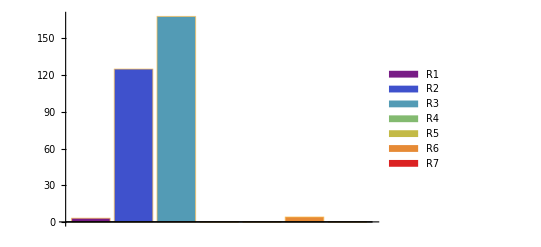

```mathematica
BarChart[numRoles,ChartLegends->{"R1","R2","R3","R4","R5","R6","R7"},ChartStyle->"Rainbow"]
```

### Definiciones de los roles universales: Nodos No Hubs: R1: Nodos ultraperiféricos R2: Nodos periféricos R3: Conectores R4: Nodos sin parentesco Nodos Hubs: R5: Provinciales R6: Conectores R7: Sin Parentesco

## Ciclos presentes en la red

Cantidad de ciclos de longitud 3 en la red: 4827

```mathematica
Length[FindCycle[red,3,All]]
```

4827

Los ciclos de mayor longitud en la red son de: 32

```mathematica
Length[Flatten[FindCycle[red,Infinity,1]]]
```

32

```mathematica
Análisis kcorecomponents: k=2,3 y 4
```

```mathematica
k1=KCoreComponents[red,2];
```

```mathematica
Length[k1]
```

1

```mathematica
Length[Flatten[k1]]
```

299

```mathematica
k2=KCoreComponents[red,3];
```

```mathematica
Length[Flatten[k2]]
```

298

```mathematica
k3=KCoreComponents[red,4];
```

```mathematica
Length[Flatten[k3]]
```

294

#### Clustering Coefficient

```mathematica
clustCoeffRedModelo=GlobalClusteringCoefficient[red];
```

```mathematica
N[clustCoeffRedModelo]
```

0.161884

#### Path: longitud promedio de todas las rutas más cortas entre vértices de la red del modelo

```mathematica
N[MeanGraphDistance[red]]
```

2.201

### Random Network

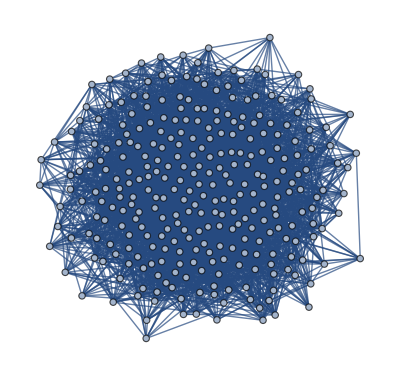

```mathematica
randNet=RandomGraph[{VertexCount[red],EdgeCount[red]}]
```

```mathematica
k4=KCoreComponents[randNet,2];
k5=KCoreComponents[randNet,3];
k6=KCoreComponents[randNet,4];
```

```mathematica
Length[k4]
```

1

```mathematica
Length[Flatten[k4]]
```

300

```mathematica
Length[k5]
```

1

```mathematica
Length[Flatten[k5]]
```

300

```mathematica
Length[Flatten[k6]]
```

300

#### Clustering Coefficient Random Network

```mathematica
N[GlobalClusteringCoefficient[randNet]]
```

0.0725806

#### Path: longitud promedio de todas las rutas más cortas entre vértices de la red aleatoria

```mathematica
N[MeanGraphDistance[randNet]]
```

2.12058

#### Ciclos en random network

```mathematica
Length[FindCycle[randNet,3,All]]
```

1698

```mathematica
Length[Flatten[FindCycle[randNet,Infinity,1]]]
```

17

Cantidad de ciclos de longitud 3 en la red aleatoria: 1698
Los ciclos de mayor longitud en la red son de: 17